```mathematica
H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});
H1=H/.{Subscript[Δ, g]->80,Subscript[Ω, 12]->15,Subscript[Ω, 23]->1}
```

{{80,15/2,0},{15/2,0,1/2},{0,1/2,Δ_r}}

```mathematica
Subscript[C, 1]=√(15*2/3)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}});
Subscript[C, 2]=√(15*1/3)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});
Subscript[C, 3]=√0.1({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}});
Subscript[C, 4]=√0.1({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,4}];
```

```mathematica
foo[δ_]:=Module[{r,H=H1/.{Subscript[Δ, r]->δ},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^4 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
]
```

```mathematica
foo[0.1]
```

{0.422619,0.158618,0.418762}

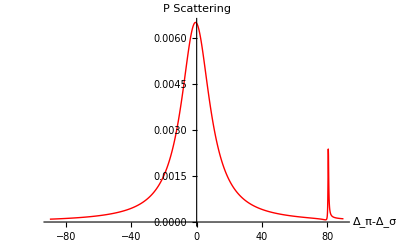

```mathematica
data=Table[{x,foo[x]},{x,-90,90,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Δ_π-Δ_σ","P Scattering"}]
```

```mathematica
foo[30]
```

{0.0533942,0.000696217,0.94591}